```mathematica
logConcentrations=Select[(Log@*QuantityMagnitude)/@ElementData[ElementData[],"CrustMolarAbundance"]//Sort,RealValuedNumberQ];
concentrations=Select[QuantityMagnitude/@ElementData[ElementData[],"CrustMolarAbundance"]//Sort,RealValuedNumberQ];
μ=Mean[logConcentrations];
σ=StandardDeviation[logConcentrations];
```

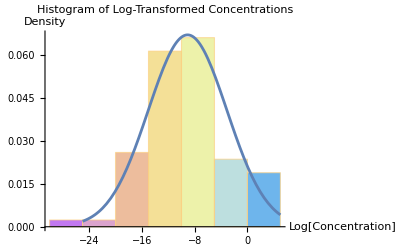

```mathematica
histLog=Show[
Histogram[logConcentrations,Automatic,"ProbabilityDensity",ChartStyle->"Pastel",PlotLabel->Style["Histogram of Log-Transformed Element Concentrations",Bold],AxesLabel->{"Log[Concentration]","Density"}],
Plot[PDF[NormalDistribution[μ,σ],x],{x,-25,5},PlotRange->All]]
```

```mathematica
(*This looks bad*)
(*hist=Show[
Histogram[concentrations,Automatic,"ProbabilityDensity",ChartStyle->"Pastel",PlotLabel->"Histogram of Concentrations (ppm)",AxesLabel->{"Concentration","Density"}],
Plot[PDF[LogNormalDistribution[μ,σ],x],{x,-25,5},PlotRange->All]]*)
```